## Figure 3

```mathematica
PLchn=Import["PL-stan-output.csv"];
WPchn=Import["WP-stan-output.csv"];
```

## the population mean parameters

```mathematica
ListParPos=38;
ChainBeg=43;
ChainEnd=1042;
```

```mathematica
PLchn[[ListParPos,8;;20]]
```

{N0_mean,mu_mean,sig_mean,pmr_mean,gamma_mean,ec50_mean,deadrateR_mean,deadrateT_mean,deadrateS_mean,recoverrateR_mean,recoverrateT_mean,recoverrateS_mean,recoverlag_mean}

```mathematica
ParPosIndx=Thread[PLchn[[ListParPos,8;;20]]->Range[8,20]]
```

{N0_mean→8,mu_mean→9,sig_mean→10,pmr_mean→11,gamma_mean→12,ec50_mean→13,deadrateR_mean→14,deadrateT_mean→15,deadrateS_mean→16,recoverrateR_mean→17,recoverrateT_mean→18,recoverrateS_mean→19,recoverlag_mean→20}

```mathematica
pars={"N_0","μ","σ","PMF","γ","EC_50","Dead_R","Dead_T","Dead_S","Recovery_R","Recovery_T","Recovery_S","lag"}
```

{N_0,μ,σ,PMF,γ,EC_50,Dead_R,Dead_T,Dead_S,Recovery_R,Recovery_T,Recovery_S,lag}

```mathematica
ylabels={"log_10number of initial parasites (N_0)","Mean age of parasites (hrs)","SD of the age of parasites (hrs)","Parasite multiplication factor (/48 hrs)","The slope constant","EC_50 of the damaged effect (ng/ml)","Dead rate of Rings", "Dead rate of Trophozoites","Dead rate of Schizonts","Recovery rate of Rings","Recovery rate of Trophozoites","Recovery rate of Schizonts","Recovery lag time (hrs)"}
```

{log_10number of initial parasites (N_0),Mean age of parasites (hrs),SD of the age of parasites (hrs),Parasite multiplication factor (/48 hrs),The slope constant,EC_50 of the damaged effect (ng/ml),Dead rate of Rings,Dead rate of Trophozoites,Dead rate of Schizonts,Recovery rate of Rings,Recovery rate of Trophozoites,Recovery rate of Schizonts,Recovery lag time (hrs)}

```mathematica
ParPosition[par_,site_]:=Position[If[StringMatchQ["PL",site],PLchn[[ListParPos]],WPchn[[ListParPos]]],s_String/;StringMatchQ[s,par]][[1,1]]
```

```mathematica
PLchnDat=PLchn[[ChainBeg;;ChainEnd,All]];
WPchnDat=WPchn[[ChainBeg;;ChainEnd,All]];
```

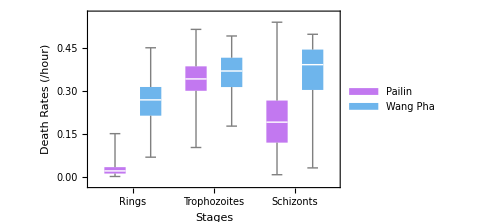

```mathematica
ddr=BoxWhiskerChart[<|
"Rings"-><|"Pailin"->PLchnDat[[All,"deadrateR_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"deadrateR_mean"/.ParPosIndx]]|>,
"Trophozoites"-><|"Pailin"->PLchnDat[[All,"deadrateT_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"deadrateT_mean"/.ParPosIndx]]|>,
"Schizonts"-><|"Pailin"->PLchnDat[[All,"deadrateS_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"deadrateS_mean"/.ParPosIndx]]|>
|>,ChartStyle->"Pastel",ChartLegends->Automatic,ChartLabels->{{"Rings","Trophozoites","Schizonts"},None},FrameLabel->{"Stages","Death Rates (/hour)"},LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"],ImageSize->Medium]
```

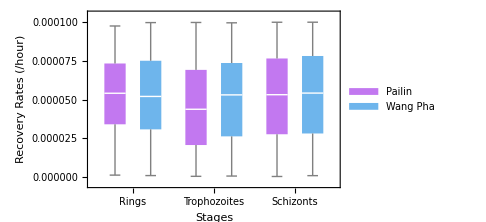

```mathematica
rcr=BoxWhiskerChart[<|
"Rings"-><|"Pailin"->PLchnDat[[All,"recoverrateR_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"recoverrateR_mean"/.ParPosIndx]]|>,
"Trophozoites"-><|"Pailin"->PLchnDat[[All,"recoverrateT_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"recoverrateT_mean"/.ParPosIndx]]|>,
"Schizonts"-><|"Pailin"->PLchnDat[[All,"recoverrateS_mean"/.ParPosIndx]],"Wang Pha"->WPchnDat[[All,"recoverrateS_mean"/.ParPosIndx]]|>
|>,ChartStyle->"Pastel",ChartLegends->Automatic,ChartLabels->{{"Rings","Trophozoites","Schizonts"},None},FrameLabel->{"Stages","Recovery Rates (/hour)"},LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"],ImageSize->Medium]
```

```mathematica
Column[{ddr,rcr}]
```

-Graphics-
-Graphics-